{{0,0}}

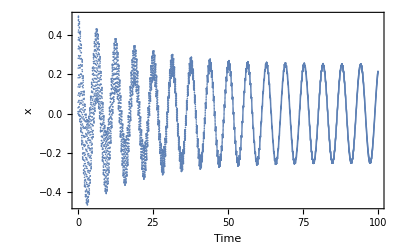

```mathematica
x = 0; 
vl = 0;
v=0; 
t = 0;
dt = 0.01;
k1=0;
k2=0;
k3=0;
k4=0;
out = {{0,0}}
For[ii = 0, ii < 10000, ii++,
k1 = -0.1*vl-4*x+Cos[t];
k2 = -0.1*(vl + k1*dt/2) - 4*x + Cos[t+dt/2];
k3= -0.1*(vl + k2*dt/2) - 4*x + Cos[t + dt/2];
k4 = -0.1*(vl + k3*dt) - 4*x + Cos[t + dt];
v = vl + (dt/6)*(k1+2k2+2k3+k4);
t = t +dt;
x = x + v;
vl = v;
res = {{t, x}};
outt = Join[out, res];
out = outt;
]
ListPlot[out, Frame->  True, PlotRange-> All, FrameStyle-> Thick, FrameLabel-> { "Time","x"}, PlotStyle->  Thick]
```